```mathematica
tbl = {4.296525, 2.146354, 1.466845, 1.100843, 1.724939, 1.454575, 1.261809, 1.110178, 1.268448, 1.214692, 1.179894, 1.227736};
tbl = tbl⟦1⟧ / tbl;
```

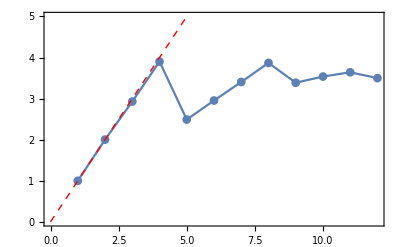

```mathematica
Show[
ListPlot[tbl, Joined->True, PlotMarkers->Automatic, Frame->True, FrameStyle->Thick, ImageSize->400, PlotRange->{Automatic, {0, 5}}],
Plot[x, {x, 0, 5}, PlotStyle->{Thick, Red, Dashed}]
]
```